```mathematica
Needs["H3`","M3/src/H.m"];
Needs["A3`","M3/src/A.m"];
```

```mathematica
cryoGIF=Map[P[#,1]/255.&,Import["M3/dat/cryo.gif","Data"],{2}];
ittCryoGIF=buildIntervalTree[cryoGIF];
```

```mathematica
Manipulate[Show[Graphics[Raster[Transpose[cryoGIF]]],showCurve[contour[cryoGIF,ittCryoGIF,t],RGBColor[1,0,0]]],{{t,.5},0,1}]
```

Show::gcomb: Could not combine the graphics objects in Show[,H3`showCurve[A3`contour[cryoGIF,ittCryoGIF,0.5],RGBColor[1, 0, 0]]].

```mathematica
volSyn=Table[N[Sin[x]Sin[y]Sin[z]],{x,0,2π,2π/10},{y,0,2π,2π/10},{z,0,2π,2π/10}];
ittVolSyn=buildIntervalTree[volSyn];
```

```mathematica
Manipulate[showSurface[contour[volSyn,ittVolSyn,t],RGBColor[1,0,0]],{{t,.5},0,1}]
```

Problem 1

```mathematica
HB=ImageData[ColorConvert[Import["M3/dat/humanbrain.png"],"Grayscale"]];
ittHB=buildIntervalTree[HB];
```

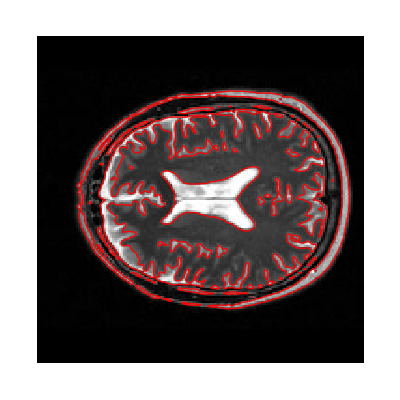
{0.247118,-Graphics-}

```mathematica
Show[Graphics[Raster[Transpose[HB]]],showCurve[contour[HB,ittHB,0.366979],RGBColor[1,0,0]]]//AbsoluteTiming
```

```mathematica
Manipulate[Show[Graphics[Raster[Transpose[HB]]],showCurve[contour[HB,ittHB,t],RGBColor[1,0,0]]],{{t,0.366979},0,1}]
```

Show::gcomb: Could not combine the graphics objects in Show[,H3`showCurve[A3`contour[HB,ittHB,0.366979],RGBColor[1, 0, 0]]].

```mathematica
CRYO=Get["M3/dat/cryo.dat"];
MM=MinMax[CRYO];
CRYO=(CRYO-MM[[1]])/(MM[[2]]-MM[[1]]);
ittCRYO=buildIntervalTree[CRYO];
```

```mathematica
Manipulate[showSurface[contour[CRYO,ittCRYO,t],RGBColor[1,0,0]],{{t,.6},0,1}]
```

```mathematica
FOOT=Get["M3/dat/foot.dat"];
MM=MinMax[FOOT];
FOOT=(FOOT-MM[[1]])/(MM[[2]]-MM[[1]]);
ittFOOT=buildIntervalTree[FOOT];
```

```mathematica
Manipulate[showSurface[contour[FOOT,ittFOOT,t],RGBColor[1,0,0]],{{t,.33},0,1}](* 0.33,0.44 *)
```